## 3-D Potentials

A very important problem in quantum mechanics concerns motion in a spherically symmetric potential V(x,y,z)=V(r) where r=√(x^2+y^2+z^2) is the distance from the origin in spherical coordinates.  As we will see, the Hamiltonian in this situation commutes with the angular momentum operators.  This in turn requires that the eigenstates of the Hamiltonian have the form ψ_nlm(r,θ,ϕ)=R_nl(r)Y_lm(θ,ϕ).

We begin by introducing the angular momentum operators (L̂)_i=1/ℏ(r̂×p̂)_i, for example (L̂)_z=1/ℏ(x̂(p̂)_y-ŷ(p̂)_x)=-ⅈ(x̂∂_y -ŷ∂_x).  Notice that I have included the factor 1/ℏ in the definition of the operators.  Angular momentum in quantum mechanics always comes in half-integer multiples of ℏ, so it is natural to always express angular momentum in units of ℏ.

First, let’s check the commutation relations.  They should obey [(L̂)_i,(L̂)_j]=ⅈ ϵ_ijk(L̂)_k, [(L̂)^2,(L̂)_i]=0.

```mathematica
Lx@f_:=-ⅈ( y D[f, z]-z D[f, y]);Ly@f_:=-ⅈ( z D[f, x]-x D[f, z]);Lz@f_:=-ⅈ( x D[f, y]-y D[f, x]);
Lsq@f_:=Lx@(Lx@f)+Ly@(Ly@f)+Lz@(Lz@f)
com[A_,B_,f_]:=A@B@f-B@A@f
```

```mathematica
com[Lx,Ly,f[x,y,z]]==  ⅈ Lz@f[x,y,z]//Simplify
com[Ly,Lz,f[x,y,z]]==  ⅈ Lx@f[x,y,z]//Simplify
com[Lz,Lx,f[x,y,z]]==  ⅈ Ly@f[x,y,z]//Simplify
com[Lsq,Lx,f[x,y,z]]== 0//Simplify
com[Lsq,Ly,f[x,y,z]]== 0//Simplify
com[Lsq,Lz,f[x,y,z]]== 0//Simplify
```

True

True

True

«3 more identical outputs»

Now, let’s check that the Hamiltonian H=(p̂)^2/(2 m)+V(r) commutes with (L̂)^2 and (L̂)_z.  First, [(L̂)^2,(p̂)^2]=[(L̂)_z,(p̂)^2]=0:

```mathematica
psq@f_:=D[f, x,x]+D[f, y,y]+D[f, z,z];
com[Lsq,psq,f[x,y,z]]==0//Simplify
com[Lz,psq,f[x,y,z]]==0//Simplify
```

True

True

Now, [(L̂)^2,V(r)]=[(L̂)_z,V(r)]=0:

```mathematica
Subscript[v_, r]@f_:=v[√(x^2+y^2+z^2)] f;
com[Lsq,Subscript[V, r],f[x,y,z]]//Simplify
com[Lz,Subscript[V, r],f[x,y,z]]//Simplify
```

0

0

To summarize: for a spherically symmetric potential the Hamiltonian Ĥ=(p̂)^2/(2 m)+V(r) commutes with  (L̂)^2 and (L̂)_z.  Thus the eigenstates of Ĥ are eigenstates of  (L̂)^2 and (L̂)_z.  Because  the  (L̂)_i obey the angular momentum commutation relations, we know from our prior work that their eigenstates obey  (L̂)^2 lm=l(l+1)lm and (L̂)_z lm=mlm.  Also, since (L̂)^2 and (L̂)_z both commute with any function of r, they operate only on angular variables and hence the position space representation of their eigenvectors must be of the form rlm=Y_lm(θ,ϕ).  We conclude that the eigenfunctions of Ĥ must be of the form ψ_nlm=R_nlm(r)Y_lm(θ,ϕ).

Our next job is to find the position representation of the angular momentum operators and eigenfunctions.  It is natural to work in spherical coordinates: {x,y,z}={r Cos[ϕ] Sin[θ],r Sin[ϕ] Sin[θ],r Cos[θ]}.

ℏ L_z=x p_y-y p_x
=-ⅈ ℏ[x ((∂r)/(∂ y)∂_r +(∂θ)/(∂y)∂_θ +(∂ϕ)/(∂ y)∂_ϕ)-y ((∂r)/(∂ x)∂_r +(∂θ)/(∂x)∂_θ +(∂ϕ)/(∂ x)∂_ϕ)]

Using (∂r)/(∂y)=-y/r, the ∂/(∂r)terms cancel.  Also, θ is independent of x and y, so (∂θ)/(∂x)=(∂θ)/(∂y)=0.  Since ϕ=ArcTan[y/x], the ∂_ϕ  terms become

```mathematica
With[{q=ArcTan[y/x]},-ⅈ (x D[q, y]-y D[q, x])] Subscript[d, ϕ]//Simplify
```

-ⅈ d_ϕ

so L_z=-ⅈ ∂_ϕ.  The eigenfunctions are ⅇ^(ⅈ m ϕ).  Note that since the eigenfunctions must be single-valued, ψ(ϕ)=ψ(ϕ+2π) requires that mbe an integer.  Thus these “orbital angular momentum” operators have only integer values of l and m.

```mathematica
Lz@f_:=-ⅈ D[f, ϕ];
Lz@(ⅇ^(ⅈ m ϕ))==m ⅇ^(ⅈ m ϕ)
```

True

ℏ L_x=y p_z-z p_y
=-ⅈ ℏ[(y (∂θ)/(∂z)-z(∂θ)/(∂y))∂_θ +(y(∂ϕ)/(∂ z)-z(∂ϕ)/(∂ y))∂_ϕ]

```mathematica
With[{phi=ArcTan[y/x],th=ArcCos[z/√(x^2+y^2+z^2)]},-ⅈ(y D[th, z]-z D[th, y])Subscript[d, θ]-ⅈ (y D[phi, z]-z D[phi, y])Subscript[d, ϕ]]/.{x->r Cos[ϕ] Sin[θ],y-> r Sin[ϕ] Sin[θ],z-> r Cos[θ]}//Simplify//PowerExpand//Simplify
```

ⅈ (Sin[ϕ] d_θ+Cos[ϕ] Cot[θ] d_ϕ)

so L_x=ⅈ  sin[ϕ]∂_θ +ⅈ cos[ϕ] cot[θ] ∂_ϕ .

ℏ L_y=z p_x-x p_z
=-ⅈ ℏ[(z(∂θ)/(∂x)-x(∂θ)/(∂z))∂_θ +(z(∂ϕ)/(∂ x)-x(∂ϕ)/(∂ z))∂_ϕ]

```mathematica
With[{phi=ArcTan[y/x],th=ArcCos[z/√(x^2+y^2+z^2)]},-ⅈ(z D[th, x]-x D[th, z])Subscript[d, θ]-ⅈ (z D[phi, x]-x D[phi, z])Subscript[d, ϕ]]/.{x->r Cos[ϕ] Sin[θ],y-> r Sin[ϕ] Sin[θ],z-> r Cos[θ]}//Simplify//PowerExpand//Simplify
```

-ⅈ (Cos[ϕ] d_θ-Cot[θ] Sin[ϕ] d_ϕ)

so L_y=-ⅈ  cos[ϕ]∂_θ +ⅈ sin[ϕ] cot[θ] ∂_ϕ .

```mathematica
Lx@f_:=ⅈ(Sin[ϕ]D[f, θ]+Cos[ϕ]Cot[θ]D[f, ϕ]);
Ly@f_:=ⅈ(-Cos[ϕ]D[f, θ]+Sin[ϕ]Cot[θ]D[f, ϕ]);
```

L_+=L_x+ⅈ L_y

```mathematica
ⅈ (Sin[ϕ] Subscript[d, θ]+Cos[ϕ] Cot[θ] Subscript[d, ϕ])+ⅈ (-ⅈ (Cos[ϕ] Subscript[d, θ]-Cot[θ] Sin[ϕ] Subscript[d, ϕ]))//Simplify
```

(Cos[ϕ]+ⅈ Sin[ϕ]) (d_θ+ⅈ Cot[θ] d_ϕ)

So the raising operator is

L_+=-ⅈ ⅇ^(ⅈ ϕ)(ⅈ ∂_θ -cot θ ∂_ϕ)

The representation of L^2=L_x^2+L_y^2+L_z^2 in spherical coordinates is

```mathematica
With[{f=Ylm[θ,ϕ]},Lx@Lx@f+Ly@Ly@f+Lz@Lz@f]//Simplify
```

-Csc[θ]^2 Ylm^(0,2)[θ,ϕ]-Cot[θ] Ylm^(1,0)[θ,ϕ]-Ylm^(2,0)[θ,ϕ]

which can be rewritten

L^2=-[1/(sin θ)∂_θ (sin θ ∂_θ)+1/(sin^2 θ)∂_ϕ^2]

Now, armed with the representation of the angular momentum operators in spherical coordinates, we find their eigenfunctions.  The basic idea should now be familiar: L_+Y_ll=0.  Using the raising operator, and using ∂_ϕ Y_ll=ⅈ L_z Y_ll=ⅈ l Y_ll,

L_+Y_ll=-ⅈ ⅇ^(ⅈ ϕ)(ⅈ ∂_θ -cot θ ∂_ϕ)Y_ll
=-ⅈ ⅇ^(ⅈ ϕ)(ⅈ ∂_θ -ⅈ l cot θ)Y_ll
→ ( ∂_θ -l cot θ)Y_(l l)=0

```mathematica
DSolve[{Yll'[th]==l Cot[th]Yll[th]},Yll[th],th]
```

{{Yll[th]→C[1] Sin[th]^l}}

so Y_(l l)=sin^l(θ)ⅇ^(ⅈ l ϕ)

```mathematica
Lminus[f_]:=ⅈ ⅇ^(-ⅈ ϕ)(-ⅈ D[f, θ]-Cot[th] D[f, ϕ])
```

Now we can use the lowering operators to get Y_(l l-1)

L_-Y_(l l)=√(l(l+1)-l(l-1))Y_(l l-1)→Y_(l l-1)= (L_-Y_(l l))/(√(2 l))

```mathematica
Lminus[Sin[th]^l ⅇ^(ⅈ l ϕ)]/√(2 l)//Simplify
```

(ⅇ^(ⅈ (-1+l) ϕ) √l Cos[th] Sin[th]^(-1+l))/(√2)

This can be repeated until we have generated all of the Y_(l m).

Normalization : ∫Sin[θ]ⅆθdϕ|Y_(l m)|^2=1.  When so normalized, the Y_lm(θ,ϕ) are called spherical harmonics and are standard functions in Mathematica. For example, Y_22 is

```mathematica
SphericalHarmonicY[2,2,θ,ϕ]
```

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

Now to work on the Hamiltonian.  In spherical coordinates, the  square of the momentum operator is:

p^2=-ℏ^2∂_r^2 -ℏ^2 2/r∂_r -ℏ^2/r^2(1/(sin θ)∂_θ (sin θ ∂_θ)+sin^2 θ∂_ϕ^2)=-ℏ^2∂_r^2 -ℏ^2 2/r∂_r +ℏ^2/r^2L^2.

For a spherically symmetric potential, ψ=R(r)Y_(l m)(θ,ϕ), and R(r) obeys

```mathematica
f
```

( p^2/(2μ)+V(r))R(r)=-ℏ^2/(2μ)(∂_r^2 +2/r∂_r)R+((ℏ^2 l(l+1))/(2μ r^2)+V(r))R=E R.

If we then define R(r)=P(r)/r, the kinetic energy term simplifies, and the Schrodinger equation becomes

```mathematica
With[{R=P[r]/r},D[R, {r,2}]+2/r D[R, r]]//Simplify//Expand
```

P''[r]/r

-ℏ^2/(2μ)∂_r^2 P+((ℏ^2 l(l+1))/(2μ r^2)+V(r))P=E P.

This is now just like a 1D potential problem.  Key point: E depends on l and a radial quantum number n, but not on m.

### Particle in a sphere

Example:  particle in a sphere, V=0 for r<a.  Setting E=ℏ^2 ϵ/μ,  the solutions to the Schrodinger equation are

```mathematica
DSolve[{-1/2 P''[r]+((l(l+1))/(2 r^2))P[r]== ϵ P[r]},P[r],r]
```

{{P[r]→√r BesselJ[1/2 (1+2 l),√2 r √ϵ] C[1]+√r BesselY[1/2 (1+2 l),√2 r √ϵ] C[2]}}

Just as in 2D, the solutions are Bessel functions, and the Y_(l+1/2) are non-zero at r=0 so, C[2]=0.  The quantization condition is J_(l+1/2)(√(2 e)a)=J_(l+1/2)(x_(l+1/2,p))=0.  Now x_(l+1/2,p)is the p^thzero of J_(l+1/2), so the number of zero crossings of J_(l+1/2)(√(2 ϵ_(n l))r) is n=p-1.  Thus

E_(n l)=ℏ^2/μ ϵ_(n l)=ℏ^2/μ 1/2((x_(l+1/2,n+1))/a)^2, n=0,1,2... . So , in units of ℏ^2/(2μ a^2), the energies are

```mathematica
elevels=Table[{l,BesselJZero[l+1/2,n+1]^2//N},{l,0,3},{n,0,5}]~Flatten~1
```

{{0,9.8696},{0,39.4784},{0,88.8264},{0,157.914},{0,246.74},{0,355.306},{1,20.1907},{1,59.6795},{1,118.9},{1,197.858},{1,296.554},{1,414.99},{2,33.2175},{2,82.7192},{2,151.855},{2,240.703},{2,349.28},{2,477.592},{3,48.8312},{3,108.516},{3,187.636},{3,286.409},{3,404.887},{3,543.088}}

```mathematica
ThadPlot[ListPlot[elevels,PlotRange->{0,300},PlotMarkers->"---"],{"l","(2  μ SuperscriptBox[a, 2 ])/ℏ^2E_(n l)"}]
```

-Graphics-

Let’s look at a p-state wavefunction, n=2

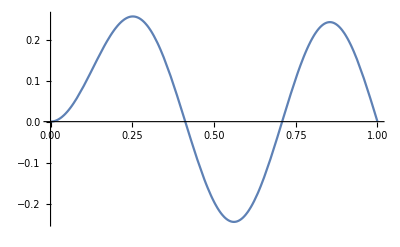

```mathematica
With[{l=1,n=2},Plot[√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]],{r,0,1}]]
```

The probability of finding the particle at a particular distance r from the center of the sphere is (P_nl(r))^2.  Our wavefunctions are so far unnormalized. The normalizing factor is the square root of

```mathematica
With[{l=1,n=2},NIntegrate[(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2,{r,0,1}]]
```

0.0289482

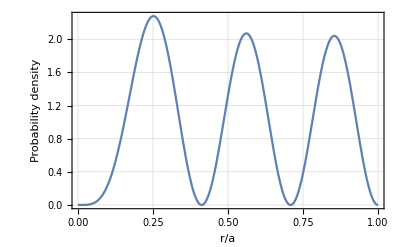

```mathematica
Module[{l=1,n=2,norm},norm=NIntegrate[(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2,{r,0,1}];ThadPlot[(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2/norm,{r,0,1},PlotRange->All,{"r/a","Probability density"}]]
```

The probability of finding the particle at a given position is |P_nl/r Y_lm|^2.  For our case of n=2,l=2, and with m=0, it is

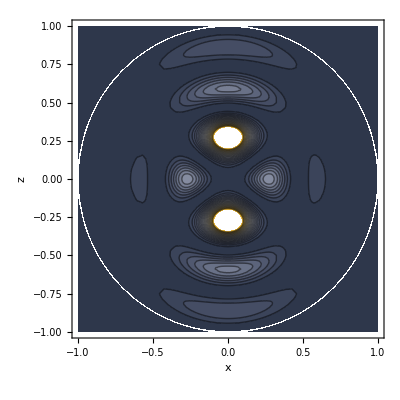

```mathematica
With[{l=2,m=0,n=2,r=√(x^2+z^2),θ=ArcCos[z/(√(x^2+z^2))]},ContourPlot[If[r>1,0,(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2/r^2 Abs[SphericalHarmonicY[l,m,θ,0]]^2],{x,-1,1},{z,-1,1},PlotRange->{0,.2},Contours->20,ColorFunction->ColorData["GrayYellowTones"]]]
```